```mathematica
root = "/pool/isilon/genomics/frandsenp/bees";
datadir = FileNameJoin[{root, "images4nets"}];
bifariousdir=FileNameJoin[{datadir, "B_bifarious"}];
melanopygusdir = FileNameJoin[{datadir, "B_melanopygus"}];
flavidir=FileNameJoin[{datadir,"B_flavifrons"}];
occidentdir=FileNameJoin[{datadir,"B_occidentalis"}];
fervidir=FileNameJoin[{datadir,"B_fervidus"}];
bifarfiles=FileNames["*.jpg", bifariousdir];
melanofiles = FileNames["*.jpg", melanopygusdir];
flavifiles=FileNames["*.jpg",flavidir];
occidentfiles=FileNames["*.jpg",occidentdir];
fervifiles=FileNames["*.jpg",fervidir];
{Length@bifarfiles, Length@melanofiles, Length@flavifiles, Length@occidentfiles,Length@fervifiles}
```

{1553,1423,1701,1288,1188}

```mathematica
Needs["CUDALink`"]
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx10g"];
```

```mathematica
bifardat=ParallelMap[Import[#]&,bifarfiles];
melanodat=ParallelMap[Import[#]&,melanofiles];
flavidat=ParallelMap[Import[#]&,flavifiles];
occidentdat=ParallelMap[Import[#]&,occidentfiles];
fervidat=ParallelMap[Import[#]&,fervifiles];
```

```mathematica
{Dimensions@bifardat, Dimensions@melanodat, Dimensions@flavidat, Dimensions@occidentdat, Dimensions@fervidat}
```

{{1553},{1423},{1701},{1288},{1188}}

```mathematica
RandomSample[bifardat, 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[melanodat,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dat=RandomSample@Join[Thread[bifardat->"bifar"],Thread[melanodat->"melano"],Thread[flavidat->"flavi"],Thread[occidentdat->"occident"],Thread[fervidat->"fervi"]];
Dimensions@dat
```

{7153}

```mathematica
RandomSample[dat,30]
```

{-Graphics-→flavi,-Graphics-→flavi,-Graphics-→fervi,-Graphics-→fervi,-Graphics-→occident,-Graphics-→flavi,-Graphics-→bifar,-Graphics-→fervi,-Graphics-→fervi,-Graphics-→fervi,-Graphics-→fervi,-Graphics-→flavi,-Graphics-→fervi,-Graphics-→occident,-Graphics-→occident,-Graphics-→flavi,-Graphics-→bifar,-Graphics-→flavi,-Graphics-→fervi,-Graphics-→melano,-Graphics-→flavi,-Graphics-→occident,-Graphics-→melano,-Graphics-→melano,-Graphics-→bifar,-Graphics-→fervi,-Graphics-→occident,-Graphics-→flavi,-Graphics-→melano,-Graphics-→flavi}

```mathematica
bifEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,bifardat];
melEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,melanodat];
flaEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,flavidat];
occEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,occidentdat];
ferEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,fervidat];
```

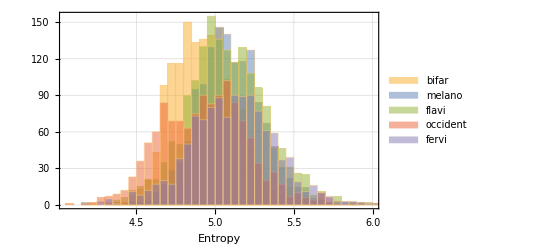

```mathematica
Histogram[{bifEntropy,melEntropy,flaEntropy,occEntropy,ferEntropy},40,ChartLegends->{"bifar","melano","flavi","occident","fervi"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

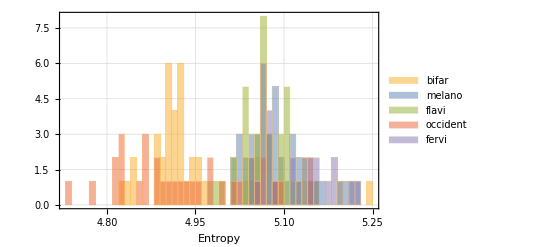

```mathematica
Histogram[{Map[Mean,Partition[bifEntropy,40]],Map[Mean,Partition[melEntropy,40]],Map[Mean,Partition[flaEntropy,40]],Map[Mean,Partition[occEntropy, 40]],Map[Mean,Partition[ferEntropy,40]]},40,ChartLegends->{"bifar","melano","flavi","occident","fervi"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

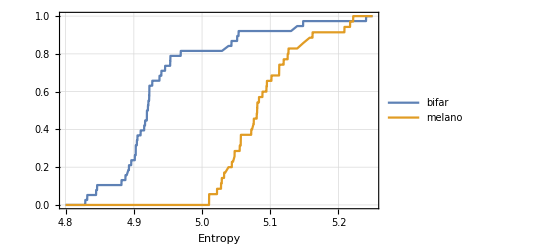

```mathematica
Plot[{CDF[EmpiricalDistribution[Map[Mean, Partition[bifEntropy,40]]],x], CDF[EmpiricalDistribution[Map[Mean, Partition[melEntropy, 40]]],x]},{x,4.8,5.25},PlotLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

```mathematica
rs=RandomSample[Range[Length[dat]]];
tix=rs[[1;;Round[Length[dat]*0.7]]];
vix=rs[[Round[Length[dat]*0.7]+1;;Round[Length[dat]*0.9]]];
ttix=rs[[Round[Length[dat]*0.9]+1;;]];
{Length@tix,Length@vix,Length@ttix}
```

{5007,1431,715}

```mathematica
networkdir=FileNameJoin[{root,"networks"}];
net=NetChain[
{
ConvolutionLayer[10,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{3,3},{2,2}],
ConvolutionLayer[20,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[40,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DropoutLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[5],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"bifar","melano","flavi","occident","fervi"}}],
"Input"->NetEncoder[{"Image",{500,298}}]
]
```

NetChain[]

```mathematica
net=NetTrain[net,dat[[tix]],ValidationSet->dat[[vix]],TargetDevice->"GPU","Method"->{"ADAM","L2Regularization"->5,"InitialLearningRate"->0.0001}];
```

```mathematica
cm=ClassifierMeasurements[net,dat[[ttix]]];
```

```mathematica
cm["Accuracy"]
```

0.921678

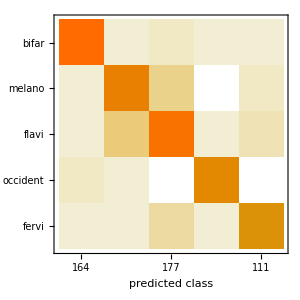

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
testDatBifar=Select[dat[[ttix]],Values@#=="bifar"&];
testDatMelano=Select[dat[[ttix]],Values@#=="melano"&];
```

```mathematica
pTestDatBifar=net[Keys@testDatBifar,{"Probability","bifar"}];
pTestDatMelano=net[Keys@testDatMelano,{"Probability","bifar"}];
```

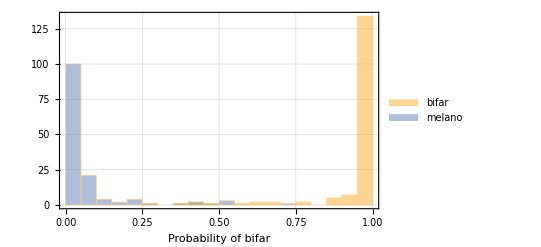

```mathematica
Histogram[{pTestDatBifar,pTestDatMelano},20,GridLines->Automatic,GridLinesStyle->Directive[Dotted,Gray],Frame->True,FrameLabel->{"Probability of bifar"},ChartLegends->{"bifar","melano"}]
```

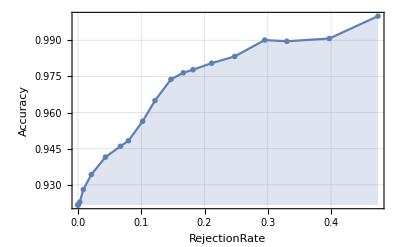

```mathematica
Show[
cm["AccuracyRejectionPlot"],
GridLines->Automatic,
GridLinesStyle->Directive[Dotted, Gray]
]
```